```mathematica
ωdef[I_,d_,T_]:=Exp[(d-I)*T]
```

```mathematica
F[ω_,σ_]:=1/2(1+Erf[(-Log[ω]-σ^2/2)/(σ*Sqrt[2])])
```

```mathematica
Fc[ω_,σ_]:=1/2(1-Erf[(-Log[ω]+σ^2/2)/(σ*Sqrt[2])])
```

```mathematica
rhs1[I_,d_,T_,σ_]:=Exp[d*T]*F[ωdef[I,d,T],σ]
```

```mathematica
rhs2[I_,d_,T_,σ_]:=Exp[I*T]*Fc[ωdef[I,d,T],σ]
```

```mathematica
lhs[f_,T_]:=Exp[f*T]
```

```mathematica
rd[I_?NumericQ,f_?NumericQ,T_?NumericQ,σ_?NumericQ]:=d/. FindRoot[0==-lhs[f,T]+rhs1[I,d,T,σ]+rhs2[I,d,T,σ],{d,0.015,0.,0.999},AccuracyGoal->8,PrecisionGoal->8,MaxIterations->1000 (*Guess,Min,Max*)]
```

```mathematica
rd[0.02,0.01,30,0.5]
```

0.0151598

```mathematica
rd[0.015159831712358837,0.01,30,0.5]
```

0.02

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

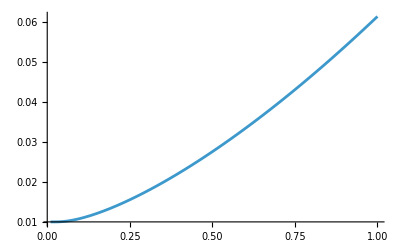

```mathematica
Plot[rd[0.012,0.01,30,σ],{σ,0.01,1.0}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

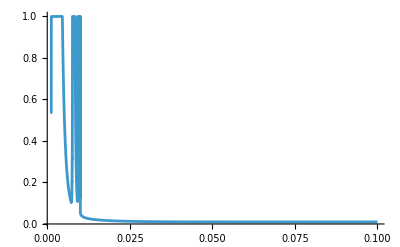

```mathematica
Plot[rd[I,0.01,30,0.5],{I,0.001,0.1},PlotRange->All]
```

```mathematica
rdeq[f_?NumericQ,T_?NumericQ,σ_?NumericQ]:=I/. FindRoot[I==rd[I,f,T,σ],{I,f+0.01,f,1},AccuracyGoal->8,PrecisionGoal->8,MaxIterations->1000 (*Guess,Min,Max*)]
```

```mathematica
rdeq[0.01,30,0.3]
```

0.0142322

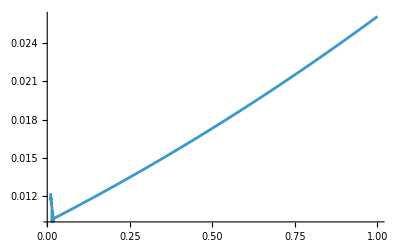

```mathematica
Plot[rdeq[0.01,30,σ],{σ,0.01,1.0}]
```

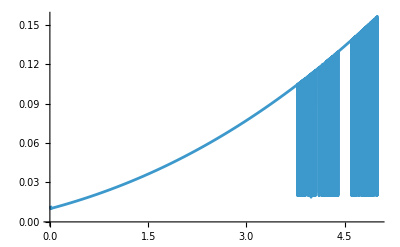

```mathematica
Plot[rdeq[0.01,30,σ],{σ,0.01,5.0}]
```